## Assignment 8

3.2.1(c)

(1) Solve  ∇^2 ϕ(x,y)=0 for the following boundary conditions Plot the solutions using Plot3D.

(c) ϕ(0,y)=2; ϕ(1,y)=ϕ(x,0)=0; (∂ϕ)/(∂y)(x,1)=1.

### Solution

To match the boundary conditions we break the problem up into two pieces, ϕ = ϕ_1+ϕ_2with the following boundary conditions on each piece:
ϕ_1(0,y)=2,    ϕ_1(1,y)=ϕ_1(x,0)=0= (∂ϕ_1)/(∂y)(x,1).
ϕ_2(0,y)=0 =ϕ_2(1,y)=ϕ_2(x,0),   (∂ϕ_2)/(∂y)(x,1)=1.

For ϕ_1 the solution must be oscillatory in the y direction and exponential in the x direction. So we take ϕ_1(x,y) = ∑_n f_n(x) g_n(y) where f_n''(x) = k_n^2 f_n(x), g_n''(y) = -k_n^2g_n(y).These forms clearly satisfy Laplace's equation.
The general solution for g_n is g_n(y) = A sin k_n y+ B cos k_n y Boundary conditions on g are g_n(0)=g_n'(1)=0. So B=0 and k_n = π (n+1/2), n=0,1,2,.... Boundary conditions on f_n(x) are such that f_n(1)=0, so we take f_n(x) = Sinh k_n(1-x). Therefore, 

		ϕ_1(x,y) = ∑_n A_n Sinh k_n(1-x) sin k_n y, 			k_n=π (n+1/2).

We choose the A_n's such that ϕ_1(0,y) = 2:

```mathematica
Clear["Global`*"]
```

```mathematica
a=1;b=1;
```

```mathematica
A[n_] = 2/b Integrate[ Sin[Pi (n+1/2) y] 2,{y,0,b}]/Sinh[Pi(n+1/2)]
```

(8 Csch[(1/2+n) π] (1+Sin[n π]))/(π+2 n π)

```mathematica
ϕ1[x_,y_] = Sum[A[n] Sinh[Pi(n+1/2) (1-x)] Sin[Pi(n+1/2) y],{n,0,20}];
```

```mathematica
Plot3D[ϕ1[x,y],{x,0,a},{y,0,b},PlotPoints->40,AxesLabel->{"x"," y","ϕ1  "}]
```

-Graphics3D-

Note the Gibb's phenomenon due to the discontinuity in the b.c.'s

Similarly for ϕ_2, ϕ_2(x,y) = ∑_n B_n sin (n π x) sinh(n π y), with B_n chosen so that (∂ϕ_2)/(∂y)(x,1)=1.

```mathematica
B[n_] = 2 Integrate[Sin[n Pi x] 1,{x,0,a}]/(n Pi Cosh[n Pi])
```

(2 (1-Cos[n π]) Sech[n π])/(n^2 π^2)

```mathematica
ϕ2[x_,y_] = Sum[B[n] Sin[n Pi x] Sinh[n Pi y],{n,1,20}];
```

```mathematica
Plot3D[ϕ2[x,y],{x,0,a},{y,0,b},PlotPoints->40,AxesLabel->{"x"," y","ϕ2  "}]
```

-Graphics3D-

Add the two  to get the full result

```mathematica
ϕ[x_,y_] = ϕ1[x,y] + ϕ2[x,y];
```

```mathematica
Plot3D[ϕ[x,y],{x,0,a},{y,0,b},PlotPoints->40,AxesLabel->{"x"," y","ϕ  "}]
```

-Graphics3D-

The boundary condition on the derivative is also matched at y=1:

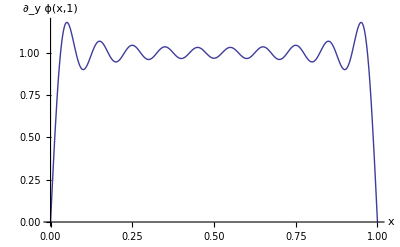

```mathematica
Plot[Evaluate[D[ϕ[x,y],y]]/.y->1,{x,0,a},AxesLabel->{"x","∂_y ϕ(x,1)\n"},PlotRange->All]
```

3.2.5(a)

(5)(a)  The bottom and top of the of the wedge shown in Fig. 3.15 are grounded, but the end at r=a is held at V=5 V. Find the potential everywhere inside the wedge by using separation of variables, and plot is as a surface plot for α=30°.

### Solution

The general solution to Laplace's equation in cylindrical coordinate is
ϕ(r,θ) = ∑_n f_n(r) g_n(θ) 
where
g_n''(θ) = -μ_n^2 g_n 
and where
1/r∂/(∂r)r(∂f_n)/(∂r)-μ^2/r^2 f_n=0. 
In this problem boundary conditions on g_n(θ) are that g_n(0)=g_n(α)=0(NOT the usual periodic boundary conditions) . The solution is g_n(θ) = sin(μ_n θ) with μ_n = n π/α.
	Turning to the radial equation, the solution to this ODE  that is finite at r=0 is 
	f_n = A_n r^μ_n. Thus,
	ϕ(r,θ) = ∑_n A_n r^(n π/α) sin(n π θ/α).
To match the boundary conditions at r=a we require

```mathematica
Clear["Global`*"]
```

```mathematica
A[n_] = 2/α Integrate[Sin[n Pi θ/α] 5,{θ,0,α}]/a^(n Pi/α)
```

-(10 a^(-(n π)/α) (-1+Cos[n π]))/(n π)

```mathematica
ϕ[r_,θ_] = Sum[A[n] r^(n Pi/α) Sin[n Pi θ/α],{n,1,20}];
```

```mathematica
α=30 Degree;a=1;
```

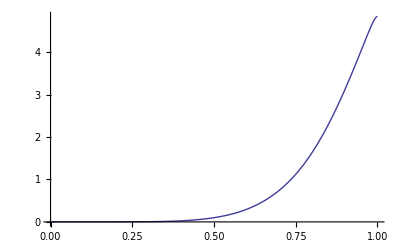

```mathematica
Plot[ϕ[r,α/2],{r,0,a},PlotRange->All]
```

```mathematica
ParametricPlot3D[{r Cos[θ], r Sin[θ], ϕ[r,θ]},{r,0,a},{θ,0,α},BoxRatios->{1,1,1},PlotRange->All,AxesLabel->{" x","y ","ϕ "},ViewPoint->{-0.849, -2.630, 1.360}]
```

-Graphics3D-

3.2.9

(9) Two concentric spheres have radii a and b (b>a). Each is divided into two hemispheres by the same horizontal plane. The upper hemisphere of the outer sphere and the lower hemisphere of the inner sphere are maintained at potential V. The other hemispheres are grounded. Determine the potential in the region a≤ r≤ b in terms of Legendre polynomials. Plot the result for b=3a/2.

### Solution

The form of the solution is

ψ(r,θ)=∑_(l=0)^∞ (A_l r^l+B_l/r^(l+1))P_l(cosθ).
Matching boundary conditions at r=a implies a set of equations given by

```mathematica
Clear["Global`*"]
```

```mathematica
Table[A[l]a^l+B[l]/a^(l+1)==Integrate[Sin[θ]LegendreP[l,0,Cos[θ]] V,{θ,Pi/2,Pi}]/Integrate[Sin[θ]LegendreP[l,0,Cos[θ]]^2,{θ,0,Pi}],{l,0,20}]
```

{A[0]+B[0]/a==V/2,a A[1]+B[1]/a^2==-(3 V)/4,a^2 A[2]+B[2]/a^3==0,a^3 A[3]+B[3]/a^4==(7 V)/16,a^4 A[4]+B[4]/a^5==0,a^5 A[5]+B[5]/a^6==-(11 V)/32,a^6 A[6]+B[6]/a^7==0,a^7 A[7]+B[7]/a^8==(75 V)/256,a^8 A[8]+B[8]/a^9==0,a^9 A[9]+B[9]/a^10==-(133 V)/512,a^10 A[10]+B[10]/a^11==0,a^11 A[11]+B[11]/a^12==(483 V)/2048,a^12 A[12]+B[12]/a^13==0,a^13 A[13]+B[13]/a^14==-(891 V)/4096,a^14 A[14]+B[14]/a^15==0,a^15 A[15]+B[15]/a^16==(13299 V)/65536,a^16 A[16]+B[16]/a^17==0,a^17 A[17]+B[17]/a^18==-(25025 V)/131072,a^18 A[18]+B[18]/a^19==0,a^19 A[19]+B[19]/a^20==(94809 V)/524288,a^20 A[20]+B[20]/a^21==0}

Matching boundary conditions at r=b implies a set of equations given by

```mathematica
Table[A[l]b^l+B[l]/b^(l+1)==Integrate[Sin[θ]LegendreP[l,0,Cos[θ]] V,{θ,0,Pi/2}]/Integrate[Sin[θ]LegendreP[l,0,Cos[θ]]^2,{θ,0,Pi}],{l,0,20}]
```

{A[0]+B[0]/b==V/2,b A[1]+B[1]/b^2==(3 V)/4,b^2 A[2]+B[2]/b^3==0,b^3 A[3]+B[3]/b^4==-(7 V)/16,b^4 A[4]+B[4]/b^5==0,b^5 A[5]+B[5]/b^6==(11 V)/32,b^6 A[6]+B[6]/b^7==0,b^7 A[7]+B[7]/b^8==-(75 V)/256,b^8 A[8]+B[8]/b^9==0,b^9 A[9]+B[9]/b^10==(133 V)/512,b^10 A[10]+B[10]/b^11==0,b^11 A[11]+B[11]/b^12==-(483 V)/2048,b^12 A[12]+B[12]/b^13==0,b^13 A[13]+B[13]/b^14==(891 V)/4096,b^14 A[14]+B[14]/b^15==0,b^15 A[15]+B[15]/b^16==-(13299 V)/65536,b^16 A[16]+B[16]/b^17==0,b^17 A[17]+B[17]/b^18==(25025 V)/131072,b^18 A[18]+B[18]/b^19==0,b^19 A[19]+B[19]/b^20==-(94809 V)/524288,b^20 A[20]+B[20]/b^21==0}

```mathematica
sol=Solve[Join[%,%%],Flatten[Table[{A[l],B[l]},{l,0,20}]]]
```

{{A[0]→V/2,B[0]→0,A[1]→(3 (a^2 V+b^2 V))/(4 (-a^3+b^3)),B[1]→(3 a^2 b^2 (a V+b V))/(4 (a^3-b^3)),A[2]→0,B[2]→0,A[3]→-(7 (a^4 V+b^4 V))/(16 (-a^7+b^7)),B[3]→-(7 a^4 b^4 (a^3 V+b^3 V))/(16 (a^7-b^7)),A[4]→0,B[4]→0,A[5]→(11 (a^6 V+b^6 V))/(32 (-a^11+b^11)),B[5]→(11 a^6 b^6 (a^5 V+b^5 V))/(32 (a^11-b^11)),A[6]→0,B[6]→0,A[7]→-(75 (a^8 V+b^8 V))/(256 (-a^15+b^15)),B[7]→-(75 a^8 b^8 (a^7 V+b^7 V))/(256 (a^15-b^15)),A[8]→0,B[8]→0,A[9]→(133 (a^10 V+b^10 V))/(512 (-a^19+b^19)),B[9]→(133 a^10 b^10 (a^9 V+b^9 V))/(512 (a^19-b^19)),A[10]→0,B[10]→0,A[11]→-(483 (a^12 V+b^12 V))/(2048 (-a^23+b^23)),B[11]→-(483 a^12 b^12 (a^11 V+b^11 V))/(2048 (a^23-b^23)),A[12]→0,B[12]→0,A[13]→(891 (a^14 V+b^14 V))/(4096 (-a^27+b^27)),B[13]→(891 a^14 b^14 (a^13 V+b^13 V))/(4096 (a^27-b^27)),A[14]→0,B[14]→0,A[15]→-(13299 (a^16 V+b^16 V))/(65536 (-a^31+b^31)),B[15]→-(13299 a^16 b^16 (a^15 V+b^15 V))/(65536 (a^31-b^31)),A[16]→0,B[16]→0,A[17]→(25025 (a^18 V+b^18 V))/(131072 (-a^35+b^35)),B[17]→(25025 a^18 b^18 (a^17 V+b^17 V))/(131072 (a^35-b^35)),A[18]→0,B[18]→0,A[19]→-(94809 (a^20 V+b^20 V))/(524288 (-a^39+b^39)),B[19]→-(94809 a^20 b^20 (a^19 V+b^19 V))/(524288 (a^39-b^39)),A[20]→0,B[20]→0}}

```mathematica
ψ[r_,θ_] = Sum[(A[l]r^l + B[l] /r^(l+1))LegendreP[l,0,Cos[θ]],{l,0,20}]/.sol[[1]]
```

V/2+((3 a^2 b^2 (a V+b V))/(4 (a^3-b^3) r^2)+(3 r (a^2 V+b^2 V))/(4 (-a^3+b^3))) Cos[θ]+1/2 (-(7 a^4 b^4 (a^3 V+b^3 V))/(16 (a^7-b^7) r^4)-(7 r^3 (a^4 V+b^4 V))/(16 (-a^7+b^7))) (-3 Cos[θ]+5 Cos[θ]^3)+1/8 ((11 a^6 b^6 (a^5 V+b^5 V))/(32 (a^11-b^11) r^6)+(11 r^5 (a^6 V+b^6 V))/(32 (-a^11+b^11))) (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)+1/16 (-(75 a^8 b^8 (a^7 V+b^7 V))/(256 (a^15-b^15) r^8)-(75 r^7 (a^8 V+b^8 V))/(256 (-a^15+b^15))) (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+1/128 ((133 a^10 b^10 (a^9 V+b^9 V))/(512 (a^19-b^19) r^10)+(133 r^9 (a^10 V+b^10 V))/(512 (-a^19+b^19))) (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)+1/256 (-(483 a^12 b^12 (a^11 V+b^11 V))/(2048 (a^23-b^23) r^12)-(483 r^11 (a^12 V+b^12 V))/(2048 (-a^23+b^23))) (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+1/1024((891 a^14 b^14 (a^13 V+b^13 V))/(4096 (a^27-b^27) r^14)+(891 r^13 (a^14 V+b^14 V))/(4096 (-a^27+b^27))) (3003 Cos[θ]-90090 Cos[θ]^3+765765 Cos[θ]^5-2771340 Cos[θ]^7+4849845 Cos[θ]^9-4056234 Cos[θ]^11+1300075 Cos[θ]^13)+1/2048(-(13299 a^16 b^16 (a^15 V+b^15 V))/(65536 (a^31-b^31) r^16)-(13299 r^15 (a^16 V+b^16 V))/(65536 (-a^31+b^31))) (-6435 Cos[θ]+255255 Cos[θ]^3-2909907 Cos[θ]^5+14549535 Cos[θ]^7-37182145 Cos[θ]^9+50702925 Cos[θ]^11-35102025 Cos[θ]^13+9694845 Cos[θ]^15)+1/32768((25025 a^18 b^18 (a^17 V+b^17 V))/(131072 (a^35-b^35) r^18)+(25025 r^17 (a^18 V+b^18 V))/(131072 (-a^35+b^35))) (109395 Cos[θ]-5542680 Cos[θ]^3+81477396 Cos[θ]^5-535422888 Cos[θ]^7+1859107250 Cos[θ]^9-3650610600 Cos[θ]^11+4071834900 Cos[θ]^13-2404321560 Cos[θ]^15+583401555 Cos[θ]^17)+1/65536(-(94809 a^20 b^20 (a^19 V+b^19 V))/(524288 (a^39-b^39) r^20)-(94809 r^19 (a^20 V+b^20 V))/(524288 (-a^39+b^39))) (-230945 Cos[θ]+14549535 Cos[θ]^3-267711444 Cos[θ]^5+2230928700 Cos[θ]^7-10039179150 Cos[θ]^9+26466926850 Cos[θ]^11-42075627300 Cos[θ]^13+39671305740 Cos[θ]^15-20419054425 Cos[θ]^17+4418157975 Cos[θ]^19)

```mathematica
a=1;b=3/2;V=1;
```

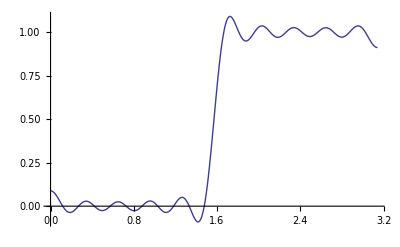

```mathematica
Plot[ψ[a,θ],{θ,0,Pi}]
```

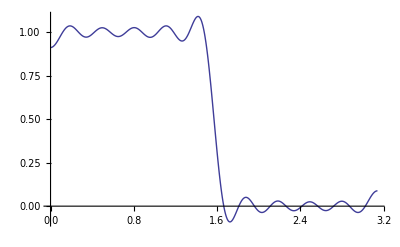

```mathematica
Plot[ψ[b,θ],{θ,0,Pi}]
```

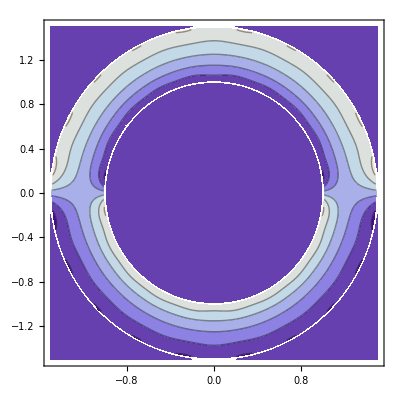

```mathematica
ContourPlot[Boole[a<Sqrt[ρ^2+z^2]<b]ψ[Sqrt[ρ^2+z^2],ArcCos[z/Sqrt[ρ^2+z^2]]],{ρ,-b,b},{z,-b,b}]
```

```mathematica
ParametricPlot3D[{r Sin[θ],r Cos[θ],ψ[r,θ]},{r,a,b},{θ,0,2Pi}]
```

-Graphics3D-

```mathematica
Limit[ψ[r,θ],b->Infinity]//Expand
```

V/2+(53228360411655 a^20 V Cos[θ])/(4503599627370496 r^20)-(1957391060625 a^18 V Cos[θ])/(140737488355328 r^18)+(36713418885 a^16 V Cos[θ])/(2199023255552 r^16)-(88297209 a^14 V Cos[θ])/(4294967296 r^14)+(7029099 a^12 V Cos[θ])/(268435456 r^12)-(293265 a^10 V Cos[θ])/(8388608 r^10)+(13125 a^8 V Cos[θ])/(262144 r^8)-(165 a^6 V Cos[θ])/(2048 r^6)+(21 a^4 V Cos[θ])/(128 r^4)-(3 a^2 V Cos[θ])/(4 r^2)+(53797647688785 a^20 V Cos[3 θ])/(4503599627370496 r^20)-(495872402025 a^18 V Cos[3 θ])/(35184372088832 r^18)+(37340998695 a^16 V Cos[3 θ])/(2199023255552 r^16)-(361215855 a^14 V Cos[3 θ])/(17179869184 r^14)+(7252245 a^12 V Cos[3 θ])/(268435456 r^12)-(153615 a^10 V Cos[3 θ])/(4194304 r^10)+(14175 a^8 V Cos[3 θ])/(262144 r^8)-(385 a^6 V Cos[3 θ])/(4096 r^6)+(35 a^4 V Cos[3 θ])/(128 r^4)+(27496575485379 a^20 V Cos[5 θ])/(2251799813685248 r^20)-(509742958725 a^18 V Cos[5 θ])/(35184372088832 r^18)+(38698853193 a^16 V Cos[5 θ])/(2199023255552 r^16)-(379053675 a^14 V Cos[5 θ])/(17179869184 r^14)+(15540525 a^12 V Cos[5 θ])/(536870912 r^12)-(171171 a^10 V Cos[5 θ])/(4194304 r^10)+(17325 a^8 V Cos[5 θ])/(262144 r^8)-(693 a^6 V Cos[5 θ])/(4096 r^6)+(28472785265925 a^20 V Cos[7 θ])/(2251799813685248 r^20)-(1065826186425 a^18 V Cos[7 θ])/(70368744177664 r^18)+(41044238235 a^16 V Cos[7 θ])/(2199023255552 r^16)-(205771995 a^14 V Cos[7 θ])/(8589934592 r^14)+(17612595 a^12 V Cos[7 θ])/(536870912 r^12)-(855855 a^10 V Cos[7 θ])/(16777216 r^10)+(32175 a^8 V Cos[7 θ])/(262144 r^8)+(29951890994025 a^20 V Cos[9 θ])/(2251799813685248 r^20)-(1138703190625 a^18 V Cos[9 θ])/(70368744177664 r^18)+(44953213305 a^16 V Cos[9 θ])/(2199023255552 r^16)-(235702467 a^14 V Cos[9 θ])/(8589934592 r^14)+(22309287 a^12 V Cos[9 θ])/(536870912 r^12)-(1616615 a^10 V Cos[9 θ])/(16777216 r^10)+(32170549586175 a^20 V Cos[11 θ])/(2251799813685248 r^20)-(627448696875 a^18 V Cos[11 θ])/(35184372088832 r^18)+(51869092275 a^16 V Cos[11 θ])/(2199023255552 r^16)-(602350749 a^14 V Cos[11 θ])/(17179869184 r^14)+(42590457 a^12 V Cos[11 θ])/(536870912 r^12)+(142469576738775 a^20 V Cos[13 θ])/(9007199254740992 r^20)-(727840488375 a^18 V Cos[13 θ])/(35184372088832 r^18)+(66688832925 a^16 V Cos[13 θ])/(2199023255552 r^16)-(1158366825 a^14 V Cos[13 θ])/(17179869184 r^14)+(165935154083985 a^20 V Cos[15 θ])/(9007199254740992 r^20)-(7521018379875 a^18 V Cos[15 θ])/(281474976710656 r^18)+(128931743655 a^16 V Cos[15 θ])/(2199023255552 r^16)+(215101125664425 a^20 V Cos[17 θ])/(9007199254740992 r^20)-(14599623913875 a^18 V Cos[17 θ])/(281474976710656 r^18)+(418881139451775 a^20 V Cos[19 θ])/(9007199254740992 r^20)

```mathematica
%/.{a->1,V->1};
```

```mathematica
ParametricPlot3D[{r Sin[θ],r Cos[θ],%},{r,1,5},{θ,0,2Pi},BoxRatios->{1,1,1/2},PlotRange->All,PlotLabel->"b -> Infinity limit",AxesLabel->{"x","z","ψ"}]
```

-Graphics3D-

```mathematica
Limit[ψ[r,θ],a->0]//Expand
```

V/2+(3 r V Cos[θ])/(4 b)-(21 r^3 V Cos[θ])/(128 b^3)+(165 r^5 V Cos[θ])/(2048 b^5)-(13125 r^7 V Cos[θ])/(262144 b^7)+(293265 r^9 V Cos[θ])/(8388608 b^9)-(7029099 r^11 V Cos[θ])/(268435456 b^11)+(88297209 r^13 V Cos[θ])/(4294967296 b^13)-(36713418885 r^15 V Cos[θ])/(2199023255552 b^15)+(1957391060625 r^17 V Cos[θ])/(140737488355328 b^17)-(53228360411655 r^19 V Cos[θ])/(4503599627370496 b^19)-(35 r^3 V Cos[3 θ])/(128 b^3)+(385 r^5 V Cos[3 θ])/(4096 b^5)-(14175 r^7 V Cos[3 θ])/(262144 b^7)+(153615 r^9 V Cos[3 θ])/(4194304 b^9)-(7252245 r^11 V Cos[3 θ])/(268435456 b^11)+(361215855 r^13 V Cos[3 θ])/(17179869184 b^13)-(37340998695 r^15 V Cos[3 θ])/(2199023255552 b^15)+(495872402025 r^17 V Cos[3 θ])/(35184372088832 b^17)-(53797647688785 r^19 V Cos[3 θ])/(4503599627370496 b^19)+(693 r^5 V Cos[5 θ])/(4096 b^5)-(17325 r^7 V Cos[5 θ])/(262144 b^7)+(171171 r^9 V Cos[5 θ])/(4194304 b^9)-(15540525 r^11 V Cos[5 θ])/(536870912 b^11)+(379053675 r^13 V Cos[5 θ])/(17179869184 b^13)-(38698853193 r^15 V Cos[5 θ])/(2199023255552 b^15)+(509742958725 r^17 V Cos[5 θ])/(35184372088832 b^17)-(27496575485379 r^19 V Cos[5 θ])/(2251799813685248 b^19)-(32175 r^7 V Cos[7 θ])/(262144 b^7)+(855855 r^9 V Cos[7 θ])/(16777216 b^9)-(17612595 r^11 V Cos[7 θ])/(536870912 b^11)+(205771995 r^13 V Cos[7 θ])/(8589934592 b^13)-(41044238235 r^15 V Cos[7 θ])/(2199023255552 b^15)+(1065826186425 r^17 V Cos[7 θ])/(70368744177664 b^17)-(28472785265925 r^19 V Cos[7 θ])/(2251799813685248 b^19)+(1616615 r^9 V Cos[9 θ])/(16777216 b^9)-(22309287 r^11 V Cos[9 θ])/(536870912 b^11)+(235702467 r^13 V Cos[9 θ])/(8589934592 b^13)-(44953213305 r^15 V Cos[9 θ])/(2199023255552 b^15)+(1138703190625 r^17 V Cos[9 θ])/(70368744177664 b^17)-(29951890994025 r^19 V Cos[9 θ])/(2251799813685248 b^19)-(42590457 r^11 V Cos[11 θ])/(536870912 b^11)+(602350749 r^13 V Cos[11 θ])/(17179869184 b^13)-(51869092275 r^15 V Cos[11 θ])/(2199023255552 b^15)+(627448696875 r^17 V Cos[11 θ])/(35184372088832 b^17)-(32170549586175 r^19 V Cos[11 θ])/(2251799813685248 b^19)+(1158366825 r^13 V Cos[13 θ])/(17179869184 b^13)-(66688832925 r^15 V Cos[13 θ])/(2199023255552 b^15)+(727840488375 r^17 V Cos[13 θ])/(35184372088832 b^17)-(142469576738775 r^19 V Cos[13 θ])/(9007199254740992 b^19)-(128931743655 r^15 V Cos[15 θ])/(2199023255552 b^15)+(7521018379875 r^17 V Cos[15 θ])/(281474976710656 b^17)-(165935154083985 r^19 V Cos[15 θ])/(9007199254740992 b^19)+(14599623913875 r^17 V Cos[17 θ])/(281474976710656 b^17)-(215101125664425 r^19 V Cos[17 θ])/(9007199254740992 b^19)-(418881139451775 r^19 V Cos[19 θ])/(9007199254740992 b^19)

```mathematica
%/.{b->1,V->1};
```

```mathematica
ParametricPlot3D[{r Sin[θ],r Cos[θ],%},{r,0,1},{θ,0,2Pi},BoxRatios->{1,1,1/2},PlotRange->All,PlotLabel->"a ->0 limit",AxesLabel->{"x","z","ψ"}]
```

-Graphics3D-

3.3.7

(7) Damped waves on a circular drumhead, radius a, satisfy the following PDE:

γ (∂z(r,θ,t))/(∂t)+(∂^2 z(r,θ,t))/(∂t^2)=c^2∇^2 z(r,θ,t), where γ>0 is a damping rate.

(a) Find the eigenmodes and eigenfrequencies for this wave equation, assuming that the edge of the drumhead at r=a  is fixed.

(b) Solve for the motion given the initial conditions z(r,θ,0)=(1-r )r^2 sin2θ , ż(r,θ,0)=0, and boundary condition z(1,θ,t)=0. Animate the solution for γ=0.3, c=1, 0<t<2.

### Solution

Eigenfunctions are the usual Bessel functions:

```mathematica
Clear["Global`*"]
```

```mathematica
ψ[m_,n_,r_,θ_] = Exp[I m θ] BesselJ[m,j[m,n] r/a]
```

ⅇ^(ⅈ m θ) BesselJ[m,(r j[m,n])/a]

But frequencies satisfy -I ω_n γ-ω_n^2=-c^2(j_(m n))^2/a^2

```mathematica
Solve[-I ω γ - ω^2 == -c^2 j[m,n]^2/a^2,ω][[1]]
```

{ω→-(ⅈ a^2 γ-√(-a^4 γ^2+4 a^2 c^2 j[m,n]^2))/(2 a^2)}

These modes are damped, with camping rate γ/2 and real frequency

```mathematica
ωr[m_,n_] =(√(-a^4 γ^2+4 a^2 c^2 j[m,n]^2))/(2 a^2)
```

(√(-a^4 γ^2+4 a^2 c^2 j[m,n]^2))/(2 a^2)

The solution will be of the form z(r,θ,t) = ∑_(m,n) ⅇ^(-γ t/2)(A_(m n) cos ω_(rm n)t + B_(m n) sin ω_(r m n)t) ψ_(m n)(r,θ).

Since the ψ_(m n)'sform an orthogonal set, we can determine the Fourier coefficients using the initial conditions. Only m=±2 will contribute.   Note that

```mathematica
D[ⅇ^(-γ t/2)(Subscript[A, m n] Cos [Subscript[ω, rm n] t] + Subscript[B, m n] Sin [Subscript[ω, r m n] t]),t]/.t->0
```

-1/2 γ A_(m n)+B_(m n) ω_(m n r)

```mathematica
a=1;γ = 0.3; c = 1;
```

```mathematica
Clear[A]
```

```mathematica
A[2,n_] := A[2,n]=Integrate[ Exp[-2 I θ]Sin[2 θ],{θ,0,2Pi}] NIntegrate[r BesselJ[2,j[2,n] r/a]r^2(1-r),{r,0,a}]/( 2 Pi BesselJ[3,j[2,n]]^2/2)
```

```mathematica
A[-2,n_] := A[-2,n]=Integrate[ Exp[2 I θ]Sin[2 θ],{θ,0,2Pi}] NIntegrate[r BesselJ[2,j[2,n] r/a]r^2(1-r),{r,0,a}]/( 2 Pi BesselJ[3,j[2,n]]^2/2)
```

```mathematica
B[m_,n_] := γ A[m,n]/(2 ωr[m,n])
```

```mathematica
j[m_,n_] := N[BesselJZero[m,n]]/; n∈Integers&&n>0
```

```mathematica
z[r_,θ_,t_] = Sum[Exp[-γ t/2]( A[m,n] Cos[ωr[m,n] t] + B[m,n] Sin[ωr[m,n] t])ψ[m,n,r,θ],{m,-2,2,4},{n,1,15}]
```

ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,5.13562 r] ((0.-0.158666 ⅈ) Cos[5.13343 t]-(0.+0.00463626 ⅈ) Sin[5.13343 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,5.13562 r] ((0.+0.158666 ⅈ) Cos[5.13343 t]+(0.+0.00463626 ⅈ) Sin[5.13343 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,8.41724 r] ((0.-0.0274344 ⅈ) Cos[8.41591 t]-(0.+0.000488973 ⅈ) Sin[8.41591 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,8.41724 r] ((0.+0.0274344 ⅈ) Cos[8.41591 t]+(0.+0.000488973 ⅈ) Sin[8.41591 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,11.6198 r] ((0.-0.0153322 ⅈ) Cos[11.6189 t]-(0.+0.000197939 ⅈ) Sin[11.6189 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,11.6198 r] ((0.+0.0153322 ⅈ) Cos[11.6189 t]+(0.+0.000197939 ⅈ) Sin[11.6189 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,14.796 r] ((0.-0.00708162 ⅈ) Cos[14.7952 t]-(0.+0.0000717965 ⅈ) Sin[14.7952 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,14.796 r] ((0.+0.00708162 ⅈ) Cos[14.7952 t]+(0.+0.0000717965 ⅈ) Sin[14.7952 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,17.9598 r] ((0.-0.00486862 ⅈ) Cos[17.9592 t]-(0.+0.000040664 ⅈ) Sin[17.9592 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,17.9598 r] ((0.+0.00486862 ⅈ) Cos[17.9592 t]+(0.+0.000040664 ⅈ) Sin[17.9592 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,21.117 r] ((0.-0.00296629 ⅈ) Cos[21.1165 t]-(0.+0.0000210709 ⅈ) Sin[21.1165 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,21.117 r] ((0.+0.00296629 ⅈ) Cos[21.1165 t]+(0.+0.0000210709 ⅈ) Sin[21.1165 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,24.2701 r] ((0.-0.00224212 ⅈ) Cos[24.2696 t]-(0.+0.0000138576 ⅈ) Sin[24.2696 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,24.2701 r] ((0.+0.00224212 ⅈ) Cos[24.2696 t]+(0.+0.0000138576 ⅈ) Sin[24.2696 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,27.4206 r] ((0.-0.00155821 ⅈ) Cos[27.4202 t]-(0.+8.52405×10^-6 ⅈ) Sin[27.4202 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,27.4206 r] ((0.+0.00155821 ⅈ) Cos[27.4202 t]+(0.+8.52405×10^-6 ⅈ) Sin[27.4202 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,30.5692 r] ((0.-0.00124505 ⅈ) Cos[30.5688 t]-(0.+6.1094×10^-6 ⅈ) Sin[30.5688 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,30.5692 r] ((0.+0.00124505 ⅈ) Cos[30.5688 t]+(0.+6.1094×10^-6 ⅈ) Sin[30.5688 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,33.7165 r] ((0.-0.000934378 ⅈ) Cos[33.7162 t]-(0.+4.15696×10^-6 ⅈ) Sin[33.7162 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,33.7165 r] ((0.+0.000934378 ⅈ) Cos[33.7162 t]+(0.+4.15696×10^-6 ⅈ) Sin[33.7162 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,36.8629 r] ((0.-0.000774536 ⅈ) Cos[36.8626 t]-(0.+3.15172×10^-6 ⅈ) Sin[36.8626 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,36.8629 r] ((0.+0.000774536 ⅈ) Cos[36.8626 t]+(0.+3.15172×10^-6 ⅈ) Sin[36.8626 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,40.0084 r] ((0.-0.000611262 ⅈ) Cos[40.0082 t]-(0.+2.29176×10^-6 ⅈ) Sin[40.0082 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,40.0084 r] ((0.+0.000611262 ⅈ) Cos[40.0082 t]+(0.+2.29176×10^-6 ⅈ) Sin[40.0082 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,43.1535 r] ((0.-0.000520147 ⅈ) Cos[43.1532 t]-(0.+1.80802×10^-6 ⅈ) Sin[43.1532 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,43.1535 r] ((0.+0.000520147 ⅈ) Cos[43.1532 t]+(0.+1.80802×10^-6 ⅈ) Sin[43.1532 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,46.298 r] ((0.-0.000425317 ⅈ) Cos[46.2978 t]-(0.+1.37798×10^-6 ⅈ) Sin[46.2978 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,46.298 r] ((0.+0.000425317 ⅈ) Cos[46.2978 t]+(0.+1.37798×10^-6 ⅈ) Sin[46.2978 t])+ⅇ^(-0.15 t+2 ⅈ θ) BesselJ[2,49.4422 r] ((0.-0.000369108 ⅈ) Cos[49.4419 t]-(0.+1.11982×10^-6 ⅈ) Sin[49.4419 t])+ⅇ^(-0.15 t-2 ⅈ θ) BesselJ[2,49.4422 r] ((0.+0.000369108 ⅈ) Cos[49.4419 t]+(0.+1.11982×10^-6 ⅈ) Sin[49.4419 t])

```mathematica
z[.4,.2,0]
```

0.0373669+0. ⅈ

check if initial conditions are matched:

```mathematica
dz[r_,θ_] = D[z[r,θ,t],t]/.t->0;
```

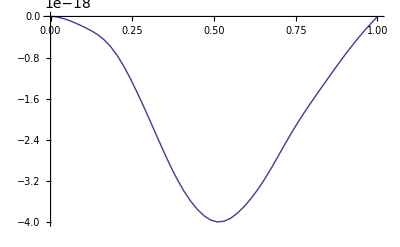

```mathematica
Plot[{dz[r,Pi/4]},{r,0,1}]
```

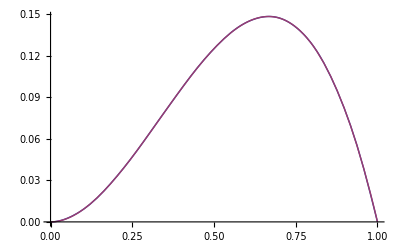

```mathematica
Plot[{z[r,Pi/4,0],r^2(1-r) Sin[2 Pi/4]},{r,0,1}]
```

I will make the animation  using the control-Y method:

```mathematica
Do[Print[ParametricPlot3D[{r Cos[θ],r Sin[θ],z[r,θ,t]},{r,0,a},{θ,0,2Pi},PlotRange->{{-1,1},{-1,1},{-.15,.15}},BoxRatios->{1,1,.4}]],{t,0,2,.1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«18 more identical outputs»

3.3.8

(8) A can of beer, radius a=3 cm and height L=11 cm, is initially at room temperature T=25 °C. The beer is placed in a cooler of ice, at 0°C.  Solve the heat equation to determine how long it takes the beer to cool to less than 5°C. Assume that the thermal diffusivity is that of water, χ=1.4×10^-7m^2/s.

### Solution

Boundary conditions are T=0. Therefore take T(r,z,t) =∑_(m,n=1)^∞ c_(m n)(t) ψ_(m n)(r,z) where ψ_(m n)(r,z) are the cylindrically -symmetric Dirichlet eigenmodes of ∇^2  in the can.These eigenmodes are
ψ_(m n)(r,z) =J_o(j_(o n) r/a) sin(m π z/L) . The corresponding eigenvalues are
λ_(m n)= -χ((j_(o n))^2/a^2+ (m π/L)^2). The Fourier coefficients have time dependence
c_(m n)(t) = A_(m n)ⅇ^(λ_(m n)t) , and A_(m n)  is given by
A_(m n) = (ψ_(m n), T(r,z,0))/(ψ_(m n),ψ_(m n)).  The solution is constructed below:

```mathematica
Clear["Global`*"]
```

```mathematica
λ[m_,n_] =-χ((j0[n]/a)^2 + (m Pi/L)^2);
ψ[m_,n_ ,r_,z_] = BesselJ[0, j0[n] r/a] Sin[m Pi z/L];
A[m_,n_] = Integrate[ 25 r ψ[m,n,r,z ],{r,0,a},{z,0,L}]/Integrate[ r ψ[m,n,r,z ]^2,{r,0,a},{z,0,L}]
```

(200 BesselJ[1,j0[n]] (-1+Cos[m π]))/((BesselJ[0,j0[n]]^2+BesselJ[1,j0[n]]^2) j0[n] (-2 m π+Sin[2 m π]))

```mathematica
j0[n_] := (BesselJZero[0,n]//N)/;n∈Integers
```

```mathematica
T[r_,z_,t_] = Sum[A[m,n] Exp[λ[m ,n] t] ψ[m,n,r,z],{m,1,10},{n,1,10}];
```

```mathematica
L = 0.11;
a = 0.03;
χ = 1.4 10^-7;
```

Temperature vs radius after 30 seconds, at z=L/2:

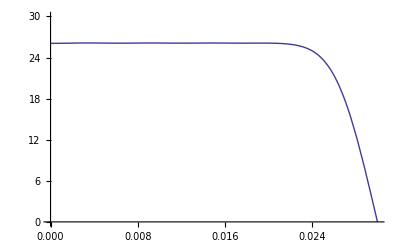

```mathematica
Plot[T[r,.055,30],{r,0,a},PlotRange->{0,30}]
```

```mathematica
T[0,L/2,40 60]
```

4.30965

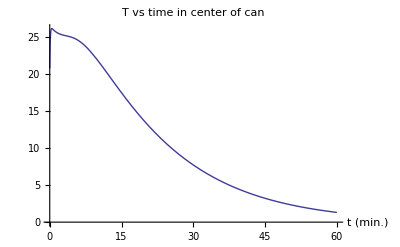

```mathematica
Plot[T[0,L/2,60 t],{t,0,60},AxesLabel->{"t (min.)",""},PlotLabel->"T vs time in center of can"]
```

It takes roughly 40 minutes to cool the center of the can to 5 Degrees. One can do better using FindRoot:

```mathematica
FindRoot[T[0,L/2,t] == 5,{t,40 60,41 60}]
```

{t→2247.84}

```mathematica
(t/.%)/60
```

37.464

3.3.14

(Hint: read problem 3.3.13)

(14)(a) A coffee cup has radius a and is filled with coffee of depth h.  Assuming potential flow and using Eq. (3.3.39) with r=(r,θ), find analytic expressions for the frequency and spatial form of the normal modes of the coffee. What is spatial form and frequency of the lowest frequency mode? (Hint: This mode is not cylindrically symmetric.) Plot the spatial form of z(r,θ,t) for this mode. 
(b) Find the frequency of this lowest mode for a cup of radius a=3 cm, filled to a depth of h=1 cm. See if you can set this mode up in your coffee. Measure its frequency with your watch, and use a ruler to determine the depth of the coffee and the cup diameter. Compare to the theory, and discuss any errors.

### Solution

The eigenmodes for the function ϕ satisfy 
∇^2 ψ_α=-ω_α^2 ψ_α, with boundary conditions n̂·∇ψ_α=0. In cylindrical geometry , these eigenmodes are given by
ψ_α(r,θ)=ⅇ^(ⅈ m θ) J_m(k_(m n) r), with eigenfrequency (ω_(m n))^2=c^2 k_(m n), and k_(m n) determined by the condition that ∂/(∂r)J_m(k_(m n) r)|_(r=a)=0.  This is as far as we can go in general. Now lets look for the lowest mode. For the m=0  modes, teh eigenvalue equation is ∂/(∂r)J_0(k_(0 n) r)|_(r=a)=0.  According to Mathematica , this derivative gives

```mathematica
D[BesselJ[0,k0[n] r],r]/.r->a
```

-BesselJ[1,k0[n]] k0[n]

Therefore, either k_(o n)=0 (constant  ψ, of no interest) or  k_(o n)=j_(1 n).

The first few zeros are given below:

```mathematica
Table[BesselJZero[1,n]//N,{n,1,5}]
```

{3.83171,7.01559,10.1735,13.3237,16.4706}

The corresponding  cylindrically symmetric modes are plotted below. The wave height for these modes is simply proportional to ψ_α, since , z_α=-h  ∇^2 ψ_α=h  ω_α^2 ψ,:

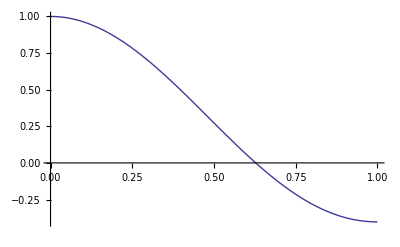
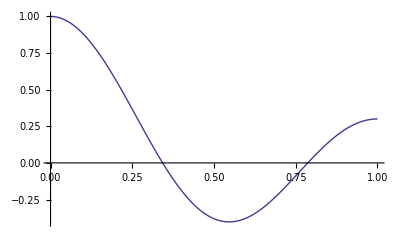
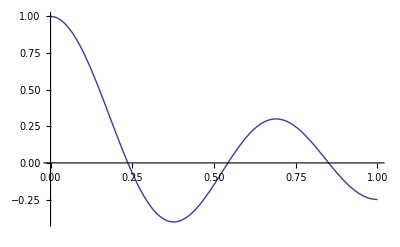
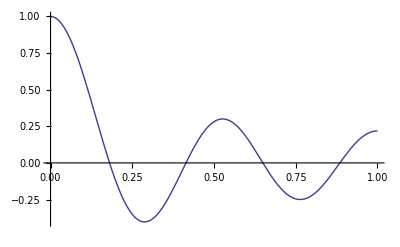
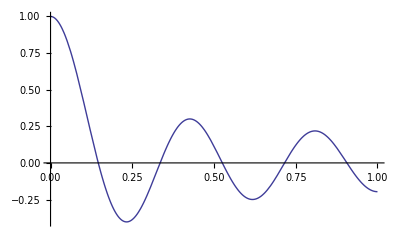

```mathematica
Table[Plot[BesselJ[0,%[[n]] r],{r,0,1}],{n,1,5}]
```

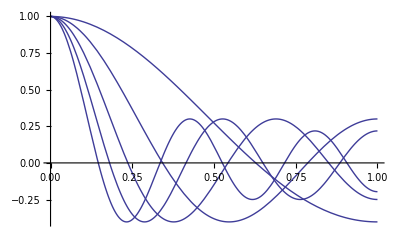

```mathematica
Show[%]
```

Now lets consider nonsymmetric modes. For m≠ 0 the mode equation is

```mathematica
D[BesselJ[m,k1[n] r],r]/.r->a
```

1/2 (BesselJ[-1+m,k1[n]]-BesselJ[1+m,k1[n]]) k1[n]

A nontrivial solution requires us to solve J_(m-1)(k_(m  n)a)=J_(m+1)(k_(m  n)a). This can be accompished using FindRoot. Graphically, solutions for k_(m n)a occur at the the crossing of the bessel functions, as shown below:

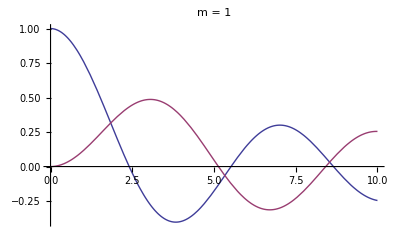
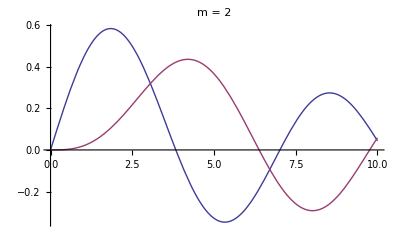
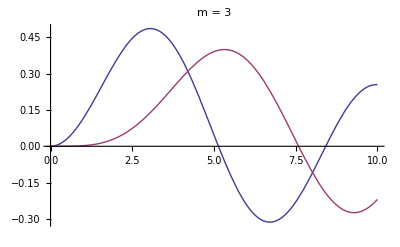
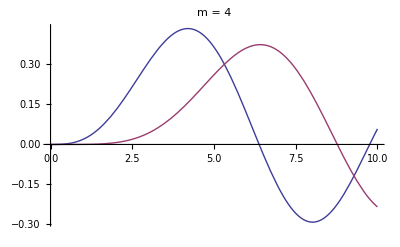

```mathematica
Table[Plot[{BesselJ[m-1,x],BesselJ[m+1,x]},{x,0,10},PlotLabel->"m = "<>ToString[m]],{m,1,4}]
```

The lowest solution is m=1, and occurs at k_(1 1) a ~ 2, which is smaller than the previous cylindrically-symetric value of 3.8371.  The next lowest solution is  an m=2 mode, with k_(2 1)a ~ 3. The 3rd lowest mode frequency is the first cylindrically-symmetric mode. The lowest mode is shown below:

```mathematica
FindRoot[BesselJ[2, k ] == BesselJ[0,k],{k,2}]
```

{k→1.84118}

```mathematica
Table[ParametricPlot3D[Evaluate[{r Cos[θ], r Sin[θ],.5BesselJ[1, k r]Cos[θ]Cos[t]}/.% ],{r,0,1},{θ,0,2 Pi},PlotRange->{{-1,1},{-1,1},{-0.5,.5}}],{t,0,1.8 Pi,.2 Pi}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[%]
```

For a=3 cm and h=1 cm, the frequency is ω = 2.62...  √(g h)/a=2.62... √(980 ·1)/3=10.4 rad/sec. The frequency in hertz is f =1.7 hertz .

The next mode is also shown below, just for the sake of interest:

```mathematica
FindRoot[BesselJ[1, k ] == BesselJ[3,k],{k,2}]
```

{k→3.05424}

```mathematica
Table[ParametricPlot3D[Evaluate[{r Cos[θ], r Sin[θ],.5BesselJ[2, k r]Cos[2θ]Cos[t]}/.% ],{r,0,1},{θ,0,2 Pi},PlotRange->{{-1,1},{-1,1},{-0.5,.5}}],{t,0,1.8 Pi,.2 Pi}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[%]
```